```mathematica
(* 1.1 Electric Fields *)
```

```mathematica
r={x,y,z};
r1={x1,y1,z1};
```

```mathematica
r-r1
```

{x-x1,y-y1,z-z1}

```mathematica
r.r1 (*dot product*)
```

x x1+y y1+z z1

```mathematica
r × r1(*cross product*)
```

{-y1 z+y z1,x1 z-x z1,-x1 y+x y1}

```mathematica
(r-r1).(r-r1)
```

(x-x1)^2+(y-y1)^2+(z-z1)^2

```mathematica
Array[v,{4,2}]
```

{{v[1,1],v[1,2]},{v[2,1],v[2,2]},{v[3,1],v[3,2]},{v[4,1],v[4,2]}}

```mathematica
MatrixForm[{{v[1,1],v[1,2]},{v[2,1],v[2,2]},{v[3,1],v[3,2]},{v[4,1],v[4,2]}}]
```

(v[1,1] | v[1,2]
v[2,1] | v[2,2]
v[3,1] | v[3,2]
v[4,1] | v[4,2])

```mathematica
EField1[r_,r1_,q1_]:=(q1/((r-r1).(r-r1))^(3/2))(r-r1)
```

```mathematica
EField1[r,r1,q1]
```

{(q1 (x-x1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(q1 (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(q1 (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2))}

```mathematica
EField1[{x,y,0},{1,1,0},1]
```

{(-1+x)/(((-1+x)^2+(-1+y)^2)^(3/2)),(-1+y)/(((-1+x)^2+(-1+y)^2)^(3/2)),0}

```mathematica
{E2D1x,E2D1y}=Take[EField1[{x,y,0},{1,1,0},1],2];
```

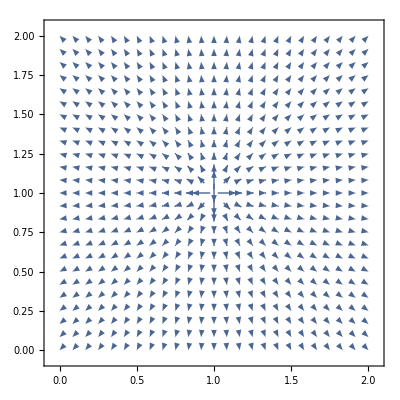

```mathematica
VectorPlot[
{E2D1x,E2D1y},{x,0,2},{y,0,2},VectorPoints->Fine
]
```

```mathematica
r2={x2,y2,z2};
```

```mathematica
EField2[r_,r2_,q2_]:=(q2/((r-r2).(r-r2))^(3/2))(r-r2)
```

```mathematica
ETotal[r_,r1_,r2_,q1_,q2_]:=EField1[r,r1,q1]+EField2[r,r2,q2]
```

```mathematica
{EDipx,EDipy}=Take[
ETotal[{x,y,0},{1,1,0},{1,1.5,0},4,-1],2
]
```

{-(-1+x)/(((-1+x)^2+(-1.5+y)^2)^(3/2))+(4 (-1+x))/(((-1+x)^2+(-1+y)^2)^(3/2)),-(-1.5+y)/(((-1+x)^2+(-1.5+y)^2)^(3/2))+(4 (-1+y))/(((-1+x)^2+(-1+y)^2)^(3/2))}

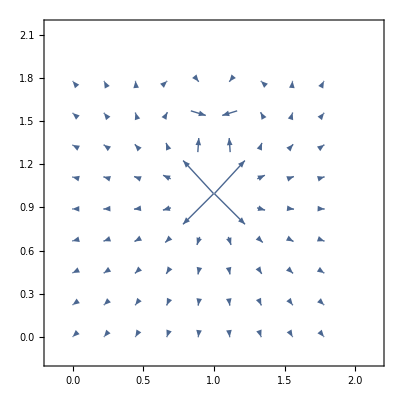

```mathematica
VectorPlot[
{EDipx,EDipy},{x,0,2},{y,0,2},VectorPoints->Coarse
]
```

```mathematica
(*field lines plotted in 3D*)

EField[r_,r3_,q3_]:=(q3/((r-r3).(r-r3))^(3/2))(r-r3);

{E3Dx,E3Dy,E3Dz}=EField[{x,y,z},{0,0,0},1]
```

{x/((x^2+y^2+z^2)^(3/2)),y/((x^2+y^2+z^2)^(3/2)),z/((x^2+y^2+z^2)^(3/2))}

```mathematica
VectorPlot3D[
{E3Dx,E3Dy,E3Dz},{x,-1,1},{y,-1,1},{z,-1,1}
]
```

-Graphics3D-

```mathematica
{E3Ddipx,E3Ddipy,E3Ddipz}=EField[{x,y,z},{0,0,-0.5},-1]+EField[{x,y,z},{0,0,0.5},1];

VectorPlot3D[
{E3Ddipx,E3Ddipy,E3Ddipz},{x,-1,1},{y,-1,1},{z,-1,1}
]
```

-Graphics3D-

```mathematica
(* 2.2 Ionic Crystals *)

α[n_]:=2*∑_(j=1)^n (-1)^(j+1)/j
Table[N[α[n]],{n,50,5000,100}]
N[α[∞]]
```

{1.36649,1.37965,1.3823,1.38344,1.38407,1.38448,1.38476,1.38496,1.38512,1.38524,1.38534,1.38543,1.38549,1.38555,1.3856,1.38565,1.38569,1.38572,1.38575,1.38578,1.38581,1.38583,1.38585,1.38587,1.38589,1.3859,1.38592,1.38593,1.38594,1.38596,1.38597,1.38598,1.38599,1.386,1.386,1.38601,1.38602,1.38603,1.38603,1.38604,1.38605,1.38605,1.38606,1.38606,1.38607,1.38607,1.38608,1.38608,1.38609,1.38609}

1.38629

```mathematica
TableForm[
Table[
{n,N[α[n]]},{n,50,5000,100}
],TableHeadings->{Table[i,{i,1,50}],{n,"α[n]"}}
]
```

| n | α[n]
1 | 50 | 1.36649
2 | 150 | 1.37965
3 | 250 | 1.3823
4 | 350 | 1.38344
5 | 450 | 1.38407
6 | 550 | 1.38448
7 | 650 | 1.38476
8 | 750 | 1.38496
9 | 850 | 1.38512
10 | 950 | 1.38524
11 | 1050 | 1.38534
12 | 1150 | 1.38543
13 | 1250 | 1.38549
14 | 1350 | 1.38555
15 | 1450 | 1.3856
16 | 1550 | 1.38565
17 | 1650 | 1.38569
18 | 1750 | 1.38572
19 | 1850 | 1.38575
20 | 1950 | 1.38578
21 | 2050 | 1.38581
22 | 2150 | 1.38583
23 | 2250 | 1.38585
24 | 2350 | 1.38587
25 | 2450 | 1.38589
26 | 2550 | 1.3859
27 | 2650 | 1.38592
28 | 2750 | 1.38593
29 | 2850 | 1.38594
30 | 2950 | 1.38596
31 | 3050 | 1.38597
32 | 3150 | 1.38598
33 | 3250 | 1.38599
34 | 3350 | 1.386
35 | 3450 | 1.386
36 | 3550 | 1.38601
37 | 3650 | 1.38602
38 | 3750 | 1.38603
39 | 3850 | 1.38603
40 | 3950 | 1.38604
41 | 4050 | 1.38605
42 | 4150 | 1.38605
43 | 4250 | 1.38606
44 | 4350 | 1.38606
45 | 4450 | 1.38607
46 | 4550 | 1.38607
47 | 4650 | 1.38608
48 | 4750 | 1.38608
49 | 4850 | 1.38609
50 | 4950 | 1.38609

```mathematica
(* madelung constant for 2D and 3D crystal *)

Mad2D[n_]:= -4∑_(j=1)^n (-1)^j/j-4∑_(j=1)^n ∑_(k=1)^n (-1)^(j+k)/(√(j^2+k^2))
Mad3D[n_]:=-6∑_(i=1)^n (-1)^i/i-12∑_(i=1)^n ∑_(j=1)^n (-1)^(i+j)/(√(i^2+j^2))-8∑_(i=1)^n ∑_(j=1)^n ∑_(k=1)^n (-1)^(i+j+k)/(√(i^2+j^2+k^2))
```

```mathematica
TableForm[
{#,N[Mad2D[#]]}&/@{10,20,100,200,400},
TableHeadings->{None,{"n","Mad2D(n)"}}
]
```

n | Mad2D(n)
10 | 1.54824
20 | 1.58105
100 | 1.60851
200 | 1.61202
400 | 1.61378

```mathematica
TableForm[
{#,N[Mad3D[#]]}&/@{10,20,30,40,60},
TableHeadings->{None,{"n","Mad3D(n)"}}
]
```

n | Mad3D(n)
10 | 1.69258
20 | 1.7194
30 | 1.72864
40 | 1.73331
60 | 1.73802

```mathematica
(*2.3 tubong curves*)
(* find a tube that follwows the shape of a curve with a given parametric equation *)
```

```mathematica
X[t_,u_,a_]:=f[t](1+(a Cos[u])/(√(f[t]^2+g[t]^2)))
Y[t_,u_,a_]:=g[t](1+(a Cos[u])/(√(f[t]^2+g[t]^2)))
Z[t_,u_,a_]:=h[t]+a Sin[u]
```

```mathematica
f[t_]:=3Cos[t]
g[t_]:=3Sin[t]
h[t_]:=0
```

```mathematica
ParametricPlot3D[
{X[t,u,1],Y[t,u,1],Z[t,u,1]},
{t,0,2π},{u,0,2π},
Axes->False,Boxed->False
]
```

-Graphics3D-

```mathematica
Clear[f,g]
```

```mathematica
f[t_]:=4Cos[t]Cos[2t]
g[t_]:=4Sin[t]Cos[2t]

ParametricPlot3D[
{X[t,u,1],Y[t,u,1],Z[t,u,1]},
{t,0,2π},{u,0,2π},
Axes->False,Boxed->False,PlotPoints->25
]
```

-Graphics3D-

```mathematica
Clear[f,g,h]

f[t_]:=3Cos[t]
g[t_]:=3Sin[t]
h[t_]:=0.5t

ParametricPlot3D[
{X[t,u,1],Y[t,u,1],Z[t,u,1]},
{t,0,6π},{u,0,2π},
Axes->False,Boxed->False,PlotPoints->40
]
```

-Graphics3D-

```mathematica
A=({{1, 1, -1, 2}, {2, -1, 1, -1}, {1, 2, -1, 1}, {1, 1, 0, -2}});
B=({{1}, {-1}, {2}, {-2}});
```

```mathematica
{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}=Inverse[A].B
```

{{-3/4},{13/4},{6},{9/4}}

```mathematica
a=Array[k,{3,3}];
b=Array[l,{3,3}];

MatrixForm[a.b]
```

(k[1,1] l[1,1]+k[1,2] l[2,1]+k[1,3] l[3,1] | k[1,1] l[1,2]+k[1,2] l[2,2]+k[1,3] l[3,2] | k[1,1] l[1,3]+k[1,2] l[2,3]+k[1,3] l[3,3]
k[2,1] l[1,1]+k[2,2] l[2,1]+k[2,3] l[3,1] | k[2,1] l[1,2]+k[2,2] l[2,2]+k[2,3] l[3,2] | k[2,1] l[1,3]+k[2,2] l[2,3]+k[2,3] l[3,3]
k[3,1] l[1,1]+k[3,2] l[2,1]+k[3,3] l[3,1] | k[3,1] l[1,2]+k[3,2] l[2,2]+k[3,3] l[3,2] | k[3,1] l[1,3]+k[3,2] l[2,3]+k[3,3] l[3,3])

```mathematica
MatrixForm[Part[a.b,1,2]]
```

k[1,1] l[1,2]+k[1,2] l[2,2]+k[1,3] l[3,2]